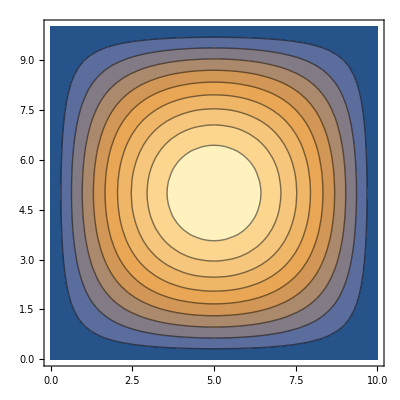

```mathematica
ψ[x_]:=√(2/L)*Sin[(nx*π)/L x];
ψ[y_]:=√(2/L)*Sin[(ny*π)/L y];

ψ[z_]:=√(2/L)*Sin[(nz*π)/L z];

nx=1;
ny=1;
nz=1;
L=10;

ContourPlot[ψ[x]ψ[y],{x,0,10},{y,0,10}]
```

```mathematica
Manipulate[ContourPlot[ψ[nx x]ψ[ny y],{x,0,10},{y,0,10}],{nx, 1,10,1},{ny,1,10,1},ControlType->PopupMenu]
```

```mathematica
Plot3D[ψ[x]ψ[y],{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[ψ[x nx]ψ[y ny],{x,0,10},{y,0,10}],{nx, 1,10,1},{ny,1,10,1},ControlType->PopupMenu]
```